# Relativistic Quantum Mechanics

By: Salazar Ángel and Potosí Quray

## Square Potential Barrier

### 1. Solving the Klein Gordon KG Equation

```mathematica
Subscript[V, 0] :=2
a := 2
ℏ :=1
m :=1
```

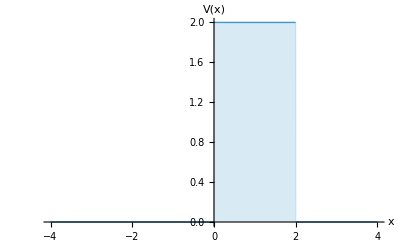

```mathematica
f[x_]:=Piecewise[{{0,x<0},{Subscript[V,0],0<=x<=a}}];
Plot[f[x],{x,-4,4},PlotStyle->Thick,AxesLabel->{"x","V(x)"},Filling->Axis]
```

#### Regions to the left and right of the barrier potential

The time-independent KG Equation has different forms in the regions to the left and right of the barrier potential:

#### First region x<0:

```mathematica
sol1 = DSolve[ Subscript[ψ, 1]''[x] == -(En^2-1 )Subscript[ψ, 1][x],Subscript[ψ, 1][x],x];
TrigToExp[sol1]
```

{{ψ_1[x]→ⅇ^(√(1-En^2) x) C[1]+ⅇ^(-√(1-En^2) x) C[2]}}

Let k1 =  √(En^2-1)

```mathematica
Subscript[ψ, 1][x_] :=A Exp[I k1 x] +B Exp[ - I k1 x]
```

#### Second Region 0<x>a

```mathematica
sol2= DSolve[ Subscript[ψ, 2]''[x]+V0 Subscript[ψ, 2][x] == -((En-V0)^2-1) Subscript[ψ, 2][x],Subscript[ψ, 2][x],x];
TrigToExp[sol2]
```

{{ψ_2[x]→ⅇ^(√(1-En^2-V0+2 En V0-V0^2) x) C[1]+ⅇ^(-√(1-En^2-V0+2 En V0-V0^2) x) C[2]}}

Let k2 =  √((E-V0)^2-1)

```mathematica
Subscript[ψ, 2][x_]:=C Exp[I k2 x]+ D Exp[-I k2 x]
```

#### Third Region x>a

```mathematica
sol3=DSolve[ Subscript[ψ, 3]''[x] == -(En^2 -1)Subscript[ψ, 3][x],Subscript[ψ, 3][x],x];
TrigToExp[sol3]
```

{{ψ_3[x]→ⅇ^(√(1-En^2) x) C[1]+ⅇ^(-√(1-En^2) x) C[2]}}

```mathematica
Subscript[ψ, 3][x_]:=F Exp[I k1 x]+G Exp[- I k1 x]/.{G->0}
```

### 2. Getting the system of equations of Boundary Conditions

We apply the matching conditions for ψ(x) and ψ’(x), that is at the points x=-a and x=a, four equations in the arbitrary constants A, B, C, D, and F will be obtained:

```mathematica
eq1 = Subscript[ψ, 1][0]==Subscript[ψ, 2][0]
```

A+B==C+D

```mathematica
eq2 = Subscript[ψ, 2][a] == Subscript[ψ, 3][a]
```

D ⅇ^(-2 ⅈ k2)+C ⅇ^(2 ⅈ k2)==ⅇ^(2 ⅈ k1) F

```mathematica
eq3 = Subscript[ψ, 1]'[-0] == Subscript[ψ, 2]'[-0]
```

ⅈ A k1-ⅈ B k1==ⅈ C k2-ⅈ D k2

```mathematica
eq4 = Subscript[ψ, 2]'[a] == Subscript[ψ, 3]'[a]
```

-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2==ⅈ ⅇ^(2 ⅈ k1) F k1

Solving the system of equations

```mathematica
Solve[{eq1,eq2,eq3,eq4},{B,C,D,F}]
```

{{B→-(A (-1+ⅇ^(4 ⅈ k2)) (-k1^2+k2^2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),C→-(2 A k1 (k1+k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),D→(2 A ⅇ^(4 ⅈ k2) k1 (k1-k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),F→-(4 A ⅇ^(-2 ⅈ k1+2 ⅈ k2) k1 k2)/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2)}}

Then we have the constant in terms of A:

```mathematica
B= - (A (-1+ⅇ^(4 ⅈ k2)) (-k1^2+k2^2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
C1= -(2 A k1 (k1+k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
D1=(2 A ⅇ^(4 ⅈ k2) k1 (k1-k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
F = -(4 A ⅇ^(-2 ⅈ k1+2 ⅈ k2) k1 k2)/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
```

Then we substitute in the Wave solutions,

```mathematica
Subscript[ψ, I][x_] :=A Exp[I k1 x] +B Exp[-I k1 x];
Subscript[ψ, II][x_]:=C1 Exp[I k2 x]+ D1 Exp[-I k2 x];
Subscript[ψ, III][x_]:=F Exp[I k1 x]+G Exp[-I k1 x]/.{G->0};
```

were,

```mathematica
k1 = √(En^2-1);
k2= √((En-V0)^2-1);
```

The reflection coefficient is given by

```mathematica
R = Abs[B/A]^2
```

Abs[((-1+ⅇ^(4 ⅈ √(-1+(En-V0)^2))) (-En^2+(En-V0)^2))/(2-En^2+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+En^2)-2 √(-1+En^2) √(-1+(En-V0)^2)-2 ⅇ^(4 ⅈ √(-1+(En-V0)^2)) √(-1+En^2) √(-1+(En-V0)^2)+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+(En-V0)^2)-(En-V0)^2)]^2

```mathematica
Rf[En_,V0_]:=Abs[((-1+ⅇ^(4 ⅈ √(-1+(En-V0)^2))) (-En^2+(En-V0)^2))/(2-En^2+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+En^2)-2 √(-1+En^2) √(-1+(En-V0)^2)-2 ⅇ^(4 ⅈ √(-1+(En-V0)^2)) √(-1+En^2) √(-1+(En-V0)^2)+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+(En-V0)^2)-(En-V0)^2)]^2
```

And the transmission coefficient is

```mathematica
T= Abs[F/A]^2
```

16 ⅇ^(4 Im[√(-1+En^2)]-4 Im[√(-1+(En-V0)^2)]) Abs[(√(-1+En^2) √(-1+(En-V0)^2))/(2-En^2+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+En^2)-2 √(-1+En^2) √(-1+(En-V0)^2)-2 ⅇ^(4 ⅈ √(-1+(En-V0)^2)) √(-1+En^2) √(-1+(En-V0)^2)+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+(En-V0)^2)-(En-V0)^2)]^2

```mathematica
Tf[En_,V0_]:=16 ⅇ^(4 Im[√(-1+En^2)]-4 Im[√(-1+(En-V0)^2)]) Abs[(√(-1+En^2) √(-1+(En-V0)^2))/(2-En^2+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+En^2)-2 √(-1+En^2) √(-1+(En-V0)^2)-2 ⅇ^(4 ⅈ √(-1+(En-V0)^2)) √(-1+En^2) √(-1+(En-V0)^2)+ⅇ^(4 ⅈ √(-1+(En-V0)^2)) (-1+(En-V0)^2)-(En-V0)^2)]^2
```

```mathematica
r1=Rf[2,5.30]
```

0.0000168412

```mathematica
t1=Tf[2,5.30]
```

0.999983

```mathematica
r1+t1
```

1.

#### Plot the reflection and transmission coefficients as a function of the Energy V

For Energy En=2

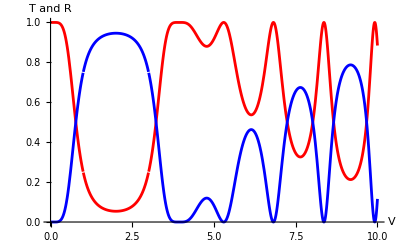

```mathematica
Plot[{Tf[2,V0],Rf[2,V0]},{V0,0,10},PlotStyle->{Red,Blue}, AxesLabel->{"V","T and R"}]
```

#### Find the roots

```mathematica
FindInstance[Rf[2.,V0]==0&&4.5≤V0≤6,V0]
```

{{V0→5.29691}}

```mathematica
FindInstance[Rf[2.,V0]==0&&6<=V0<=8,V0]
```

{{V0→6.81732}}

```mathematica
FindInstance[Rf[2.,V0]==0&&8<=V0<=9,V0]
```

{{V0→8.36227}}

```mathematica
FindInstance[Rf[2.,V0]==0&&9<=V0<=10,V0]
```

{{V0→9.91739}}

Summary Table

```mathematica
{{V0},{5.296908309475615},{6.817323935802019},{8.36226513156733},{9.917387669352088}}//TableForm
```

V0
5.29691
6.81732
8.36227
9.91739